```mathematica
Quit[]
```

README:
This Notebook contains the calculations performed in Appendix C of arXiv:2605.16168.

In that article, we find solutions to consistent truncations of supergravity where some real scalars are analytically extended to imaginary values, ensuring the metric remains real-valued. Among the solutions there are Lorentzian traversable wormholes connecting two asymptotically Anti-de Sitter spacetimes and flows that have a real metric also when uplifted to ten or eleven dimensions. We argue that the holographic duals are pseudo-Hermitian and PT-symmetric theories. Wormhole solutions also admit an interpretation as the low-energy theory of two stacks of branes and antibranes after tachyon condensation. The wormhole is then dual to an entangled state of two copies of the theory that lives on a stack of branes. We present some evidence by computing the mutual information between the theories at each boundary and by identifying the Goldstone bosons associated to the breaking of the two copies of Poincaré symmetry to their diagonal subgroup.

Even though the solutions we construct satisfy a set of BPS equations and can be seen as analytic extensions of supersymmetric solutions, their stability is not guaranteed. In this Notebook we study the perturbative stability of 3 examples of ghost scalars coupled to gravity, listed in the section 2.2 of arXiv:2605.16168. 

In the three cases that we examine, we find no evidence of instability.

The methodology is briefly explained at the start of each example and in much more detail in Appendix B and C of arXiv:2605.16168.

Authors of the article: Jose M. Begines, Antón F. Faedo, Carlos Hoyos, Daniele Musso
Developers of the Notebook: Carlos Hoyos, Daniele Musso

Notation:
- The squared mass M^2 of the paper is denoted in the present notebook with λ.

Each example constitutes an independent code. Quit the kernel before running.

# Stability Analysis

d+1=5 Wormholes 𝒩==4 SYM Coulomb branch (Example 1)

Methodology:
We employ a spectral method based on Chebyshev polynomials.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain.

We then analyze the asymptotic behavior of the solutions at the two endpoints, υ = -1 and υ = 0. This allows us to explicitly factor out the corresponding regular asymptotic behavior at each endpoint. We subsequently introduce a new radial coordinate s ∈ [-1,1], which provides the standard domain for the Chebyshev expansion. 

The radial domain is discretized on a Gauss-Lobatto grid. This yields a convenient and efficient construction of discretized radial first- and second-order derivatives. Since the regular asymptotics have been factored out, no additional boundary conditions need to be imposed. The spectrum is then obtained by solving the resulting discretized generalized eigenvalue problem.

## Background

Superpotential:

```mathematica
W[η_]=6/L Cos[η/(√3)];
```

Potential from superpotential:

```mathematica
d=4;
V[η_]=-1/2 W'[η]^2-d/(4(d-1))W[η]^2//Simplify
```

-(3 (3+Cos[(2 η)/(√3)]))/L^2

Background profile of the scalar ghost:

```mathematica
η0[r_]=2 √3 ArcTan[ⅇ^(2(r-r0)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=2 Cosh[(2 (r-r0))/L];
```

## Z_η fluctuation

Equation of motion. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2):

```mathematica
eqZη=Zη''[r]+(2 a'[r])/a[r] Zη'[r]+((w^2-k^2)/a[r]-(4 a[r] V'[η0[r]] η0'[r])/(3 a'[r])-4/3 η0'[r]^2-(2 a[r]^2 η0'[r]^4)/(9 a'[r]^2)+V''[η0[r]])Zη[r] /.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify
```

((4 ⅇ^((12 r)/L)+4 ⅇ^((12 r0)/L)-36 ⅇ^((4 (2 r+r0))/L)-36 ⅇ^((4 (r+2 r0))/L)-2 ⅇ^((6 (r+r0))/L) λ+ⅇ^((2 (5 r+r0))/L) λ+ⅇ^((2 (r+5 r0))/L) λ) Zη[r])/((ⅇ^((4 r)/L)-ⅇ^((4 r0)/L))^2 (ⅇ^((4 r)/L)+ⅇ^((4 r0)/L)) L^2)+(4 (ⅇ^((4 r)/L)-ⅇ^((4 r0)/L)) Zη'[r])/((ⅇ^((4 r)/L)+ⅇ^((4 r0)/L)) L)+Zη''[r]

Change of radial coordinate (compactification):

```mathematica
rv[v_]=r0+L Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^((rr-r0)/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zη[r_]=zη[vr[r]];

eqzη=Collect[Simplify[(4 L^2)/((v^2-1)^2)eqZη/.r->rv[v]],{zη''[v],zη'[v],zη[v],λ},FullSimplify]
```

((-2+24 v^2+20 v^4+24 v^6-2 v^8)/(v^2 (-1+v^4)^2)+(2 λ)/(1+6 v^2+v^4)) zη[v]+(2 v (-15-10 v^2+v^4) zη'[v])/(-1-5 v^2+5 v^4+v^6)+zη''[v]

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem.

```mathematica
c1=Coefficient[eqzη,zη'[v]];
c0=Coefficient[eqzη,zη[v]];
```

Asymptotic study about v==-1:

```mathematica
c1vm1=Series[c1,{v,-1,-1}]
c0vm1=Series[c0,{v,-1,-2}]

DSolve[zη''[v]+Normal[c1vm1] zη'[v]+Normal[c0vm1] zη[v]==0,zη[v],v]//Flatten
```

-3/(v+1)+O[v+1]^0

4/(v+1)^2+1/O[v+1]

{zη[v]→(1+v)^2 C[1]+2 (1+v)^2 C[2] Log[1+v]}

Asymptotic study about v==0:

```mathematica
c1v0=Series[c1,{v,0,-1}]
c0v0=Series[c0,{v,0,-2}]

DSolve[zη''[v]+Normal[c1v0] zη'[v]+Normal[c0v0] zη[v]==0,zη[v],v]//Flatten
```

O[v]^1

-2/v^2+1/O[v]

{zη[v]→C[1]/v+v^2 C[2]}

We factor out explicitly the regular behaviours at both asymptotic regions:

```mathematica
zη[v_]=v^2(1+v)^2 ψv[v];
```

We change the radial coordinate so that the domain coincides with the domain of Chebyshev polynomials s∈[-1,1]. We also multiply the equation for the singular factor (1-s^2).

```mathematica
vs[s_]=(s-1)/2;
ψv[v_]=ψ[2v+1];
```

```mathematica
eqψ=Collect[((1-s)(1+s)eqzη/.v->vs[s])/Coefficient[eqzη/.v->vs[s],ψ''[s]],{ψ''[s],ψ'[s],ψ[s],λ},FullSimplify]
```

(-18-32/(-3+s)^2+28/(-3+s)-(64 (-3+s))/(5+(-2+s) s)^2-32/(5+(-2+s) s)-(32 (-41+s (39+(-15+s) s)))/(41+(-2+s) s (26+(-2+s) s))+((8-8 s^2) λ)/(41+(-2+s) s (26+(-2+s) s))) ψ[s]+(-2+24/(-3+s)-10 s+(32 (7+s+3 (-1+s) s^2))/(41+(-2+s) s (26+(-2+s) s))) ψ'[s]+(1-s^2) ψ''[s]

## Numerics (Chebyshev spectral method)

We define the coefficients of the discretized matrix.

```mathematica
Clear[A0,A1,B0,B1,S0];

S0[s_]=Coefficient[eqψ,ψ''[s]];
A0[s_]=Coefficient[eqψ,ψ'[s]]/.λ->0;
A1[s_]=Coefficient[Coefficient[eqψ,ψ'[s]],λ];
B0[s_]=Coefficient[eqψ,ψ[s]]/.λ->0;
B1[s_]=Coefficient[Coefficient[eqψ,ψ[s]],λ];
```

Gauss-Lobatto grid:

```mathematica
chebGrid[n_]:=N[Cos[Pi Range[0,n]/n],100];
```

Matrices for first and second derivative:

```mathematica
chebD[n_,prec_: MachinePrecision]:=Module[{x,c,D,X,C,dX},
x=N[Cos[Pi Range[0,n]/n],prec];
c=Join[{2},ConstantArray[1,n-1],{2}]*(-1)^Range[0,n];
(*Build matrices*)
X=Outer[Subtract,x,x];
C=Outer[Times,c,1/c];
(*Add identity to avoid division by zero*)
dX=X+IdentityMatrix[n+1];
D=C/dX;
(*Fix diagonal*)
D=D-DiagonalMatrix[Total[D,{2}]];
D]
```

Discretized problem:

```mathematica
buildMatrices[NN_]:=Module[{s,S0v,A0v,A1v,B0v,B1v,M0,M1,n1},(*Work with packed interior grid*)
n1=NN+1;
s=Developer`ToPackedArray[chebGrid[NN]];
(*Vectorized evaluation (no Table!)*)
S0v=Developer`ToPackedArray[S0/@s];
A0v=Developer`ToPackedArray[A0/@s];
A1v=Developer`ToPackedArray[A1/@s];
B0v=Developer`ToPackedArray[B0/@s];
B1v=Developer`ToPackedArray[B1/@s];
(*Replace DiagonalMatrix[v].D with fast row scaling*)
D1=chebD[NN,100];
D2=D1.D1;
M0=S0v*D2+A0v*D1;
M0=M0+DiagonalMatrix[B0v];
M1=A1v*D1+DiagonalMatrix[B1v];

{M0,M1}]
```

Function which computes of the first ten eigenvalues for M^2 in the normal mode spectrum:

```mathematica
computeQNMs[NN_]:=Module[{M0,M1,vals},{M0,M1}=buildMatrices[NN];
vals=Eigenvalues[{M0,-M1},-10];
vals];
```

First 10 eigenvalues M^2 computed with 100 and 200 collocation points:

```mathematica
modes100=N[Sort[computeQNMs[100]],5]
```

{13.397,53.933,117.15,203.3,312.41,444.48,599.52,777.53,978.51,1202.5}

```mathematica
modes200=N[Sort[computeQNMs[200]],5]
```

{13.397,53.933,117.15,203.3,312.41,444.48,599.52,777.53,978.51,1202.5}

d+1=4 Wormholes ABJM Coulomb branch (Example 2)

Methodology:
This example can be treated analytically.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain.

The resulting ODE can be solved analytically (not all versions of Mathematica are able to find the analytical solution: we employed Mathematica 11, while more recent versions, such as Mathematica 13 and 14, did not find an analytical solution). 

The spectrum is obtained by imposing regularity in the interior and a vanishing source at the boundary (in the alternative quantization).

## Background

Superpotential:

```mathematica
W[η_]=4/L Cos[η/2];
```

Potential from superpotential:

```mathematica
d=3;
V[η_]=-1/2 W'[η]^2-d/(4(d-1))W[η]^2//Simplify
```

-(2 (2+Cos[η]))/L^2

Background profile of the scalar ghost:

```mathematica
η0[r_]=4ArcTan[ⅇ^((r-r0)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=4 Cosh[(r-r0)/L]^2;
```

## Z_η fluctuation

Equation of motion. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2):

```mathematica
eqZη=Zη''[r]+(3 a'[r])/(2a[r])Zη'[r]+ ((w^2-k^2)/a[r]-(2 a[r] V'[η0[r]] η0'[r])/a'[r]-3/2 η0'[r]^2-(a[r]^2 η0'[r]^4)/(2 a'[r]^2)+V''[η0[r]])Zη[r]/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify
```

((2 ⅇ^((8 r)/L)+2 ⅇ^((8 r0)/L)+ⅇ^((2 (3 r+r0))/L) (-8+λ)+ⅇ^((2 (r+3 r0))/L) (-8+λ)-2 ⅇ^((4 (r+r0))/L) (10+λ)) Zη[r])/((ⅇ^((4 r)/L)-ⅇ^((4 r0)/L))^2 L^2)+(3 (ⅇ^((2 r)/L)-ⅇ^((2 r0)/L)) Zη'[r])/((ⅇ^((2 r)/L)+ⅇ^((2 r0)/L)) L)+Zη''[r]

Change of radial coordinate (compactification):

```mathematica
rv[v_]=r0+L Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^((rr-r0)/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zη[r_]=zη[vr[r]];

eqzη=Collect[Simplify[(4 L^2)/((v^2-1)^2)eqZη/.r->rv[v]],{zη''[v],zη'[v],zη[v],λ},FullSimplify]
```

(-(2 (1-6 v^2+v^4))/(v^2 (-1+v^2)^2)+λ/((1+v^2)^2)) zη[v]+(2 v (-5+v^2) zη'[v])/(-1+v^4)+zη''[v]

Analytical solution of eqzη (found with Mathematica 11 but apparently not found by versions 13 and 14):

```mathematica
solzη[v_]=-1/(8 v (1+v^2) √(4+λ) Abs[λ])ⅇ^(-(ⅈ λ (2 (4+λ) ArcTan[v]+√2 (((-4-λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))-((4+λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))))/(2 √(λ^2 (4+λ)))) (-1+v^2) √(2+2 v^2+λ-√λ √(4+λ)) √(2+2 v^2+λ+√λ √(4+λ)) (8 ⅇ^((ⅈ λ (2 (4+λ) ArcTan[v]+√2 (((-4-λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))-((4+λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))))/(√(λ^2 (4+λ)))) √(4+λ) Abs[λ] C[1]+ⅈ C[2]);
```

```mathematica
Simplify[eqzη/.zη->solzη](*check that it is actually a solution*)
```

0

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem.

Expansion about the throat of the wormhole:

```mathematica
sZϕWorm=Series[solzη[v],{v,0,2}]
```

(√(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)) (8 √(4+λ) Abs[λ] C[1]+ⅈ C[2]))/(8 √(4+λ) Abs[λ] v)+((-2+λ) (8 √(4+λ) Abs[λ] C[1]+ⅈ C[2]) v)/(4 √(4+λ) √(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)) Abs[λ])+(2 (32 ⅈ λ^2 √(4+λ) Abs[λ] C[1]+8 ⅈ λ^3 √(4+λ) Abs[λ] C[1]+4 λ^2 C[2]+λ^3 C[2]) v^2)/(3 √(4+λ) √(λ^2 (4+λ)) (2+λ-√λ √(4+λ))^(3/2) (2+λ+√λ √(4+λ))^(3/2) Abs[λ])+O[v]^3

Regularity requirement at v==0

```mathematica
solc2=Solve[SeriesCoefficient[sZϕWorm,{v,0,-1}]==0,C[2]]//Flatten
```

{C[2]→8 ⅈ √(4+λ) Abs[λ] C[1]}

```mathematica
Assuming[λ >0,sZϕWorm/.solc2/.C[1]->-I AA//FullSimplify]
```

4/3 AA λ √(4+λ) v^2+O[v]^3

```mathematica
Assuming[λ <0,sZϕWorm/.solc2/.C[1]->-I AA//FullSimplify]
```

-2/3 (AA λ √(4+λ) √(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ))) v^2+O[v]^3

Expansion about the (negative) boundary of the wormhole:

```mathematica
solzη[-1]
```

0

```mathematica
sZϕBoun=Series[solzη[v]/.solc2/.C[1]->-I AA,{v,-1,2}];
```

```mathematica
C1=SeriesCoefficient[sZϕBoun,1];
C2=SeriesCoefficient[sZϕBoun,2];
```

```mathematica
subleading=Assuming[λ  ∈ Reals,C2/C1//Simplify//TrigToExp//Factor//FullSimplify]
```

1/2 (1+(λ Cot[(λ (-1/2 π (4+λ)+(√2 (4+λ-√λ √(4+λ)) ArcTan[(√2)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))+(√2 (4+λ+√λ √(4+λ)) ArcTan[(√2)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ)))))/(2 √(λ^2 (4+λ)))])/(√(4+λ) Sign[λ]))

Asking the ratio C2/C1=0 corresponds to a vanishing subleading fall-off. Since we are working in the alternative quantization, this amounts to zero dual source.

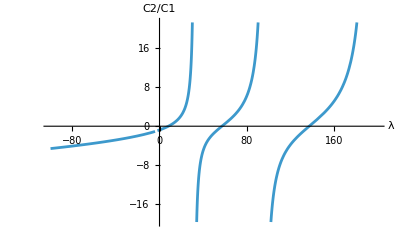

```mathematica
Plot[subleading,{λ,-100,200},AxesLabel->{"λ","C2/C1"}]
```

```mathematica
FindRoot[subleading==0,{λ,10}]
```

{λ→8.14752}

```mathematica
FindRoot[subleading==0,{λ,50}]
```

{λ→57.2625}

```mathematica
FindRoot[subleading==0,{λ,150}]
```

{λ→137.374}

d+1=5 Wormholes 𝒩==1^* SYM GPPZ, two scalars (Example 5)

Methodology:
This example involves two scalar fields and the coupled ODEs governing their fluctuations.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE system has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain.

We then analyze the asymptotic behavior of the solutions at the two endpoints, υ = -1 and υ =0. This allows us to explicitly factor out the corresponding regular asymptotic behavior at each endpoint. We subsequently introduce a new radial coordinate s ∈ [-1,1]. 

We solve the coupled system numerically. Specifically, we match two numerical solutions propagated, respectively, from the two endpoints of the radial domain. We obtain the spectrum requiring the determinant of the matching matrix, constructed from the numerical solutions and their derivatives, to vanish at a specified point in the interior of the integration domain. This determinant constitutes a generalization of the Wronskian to the coupled system.

Notation:
- For ease of notation, the fields η^1 and η^2 in the paper are here denoted with χ and α, respectively.

## Background

Superpotential:

```mathematica
W[χ_,α_]=3/L (Cos[χ/(√3)]+Cos[α]);
```

Potential from superpotential:

```mathematica
d=4;
V[χ_,α_]=-1/2(D[ W[χ,α],χ]^2+D[ W[χ,α],α]^2)-d/(4(d-1))W[χ,α]^2//FullSimplify
```

-(3 (8-Cos[2 α]+8 Cos[α] Cos[χ/(√3)]+Cos[(2 χ)/(√3)]))/(4 L^2)

Background profile of the scalar ghosts:

```mathematica
χ0[r_]=2 √3 ArcTan[ⅇ^((r-r1)/L)];
α0[r_]=2ArcTan[ⅇ^(3(r-r2)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=2^(4/3) Cosh[(r-r1)/L] Cosh[3 (r-r2)/L]^(1/3);
```

## Z_χ and Z_α fluctuation equations

We have already set the scalar, gauge-invariant combination of the metric to zero, H_S=0. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2).

```mathematica
eqZχ=Collect[(2 a'[r] Zχ'[r])/a[r]+Zχ''[r]+Zα[r] (-(2 χ0'[r] (α0'[r] (6 a'[r]^2+a[r]^2 (α0'[r]^2+χ0'[r]^2))+3 a[r] a'[r] Derivative[0,1][V][χ0[r],α0[r]])+6 a[r] a'[r] α0'[r] Derivative[1,0][V][χ0[r],α0[r]])/(9 a'[r]^2)+Derivative[1,1][V][χ0[r],α0[r]])+Zχ[r] ((-k^2+w^2)/a[r]-4/3 χ0'[r]^2-(2 a[r]^2 χ0'[r]^2 (α0'[r]^2+χ0'[r]^2))/(9 a'[r]^2)-(4 a[r] χ0'[r] Derivative[1,0][V][χ0[r],α0[r]])/(3 a'[r])+Derivative[2,0][V][χ0[r],α0[r]])/.{r1->0,r2->0}/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify,{Zχ''[r],Zχ'[r],Zχ[r],Zα[r],λ},Simplify];
```

```mathematica
eqZα=Collect[(2 a'[r] Zα'[r])/a[r]+Zα''[r]+Zα[r] ((-k^2+w^2)/a[r]-4/3 α0'[r]^2-(2 a[r]^2 α0'[r]^2 (α0'[r]^2+χ0'[r]^2))/(9 a'[r]^2)-(4 a[r] α0'[r] Derivative[0,1][V][χ0[r],α0[r]])/(3 a'[r])+Derivative[0,2][V][χ0[r],α0[r]])+Zχ[r] (-(2 χ0'[r] (α0'[r] (6 a'[r]^2+a[r]^2 (α0'[r]^2+χ0'[r]^2))+3 a[r] a'[r] Derivative[0,1][V][χ0[r],α0[r]])+6 a[r] a'[r] α0'[r] Derivative[1,0][V][χ0[r],α0[r]])/(9 a'[r]^2)+Derivative[1,1][V][χ0[r],α0[r]])/.{r1->0,r2->0}/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify,{Zα''[r],Zα'[r],Zα[r],Zχ[r],λ},Simplify];
```

Change of radial coordinate (compactification):

```mathematica
rv[v_]=L/2 Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^(2 rr/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zχ[r_]=zχ[vr[r]];
Zα[r_]=zα[vr[r]];

eqzχ=Assuming[-1<v<1,Collect[Simplify[L^2/((1-v^2)^2)eqZχ/.r->rv[v]],{zχ''[v],zχ'[v],zχ[v],zα[v],λ},FullSimplify]]
eqzα=Assuming[-1<v<1,Collect[Simplify[L^2/((1-v^2)^2)eqZα/.r->rv[v]],{zα''[v],zα'[v],zα[v],zχ[v],λ},FullSimplify]]
```

(√3 (-1-5 v^2-11 v^4+v^6) zα[v])/(2 (1+3 v^2) (v+v^3)^2)+((-1+3 v^2+28 v^4+28 v^6+37 v^8+v^10)/(2 v^2 (1+3 v^2) (-1+v^4)^2)-λ/(2 (-1+v^2) (2+6 v^2)^(1/3))) zχ[v]+(2 v (3+v^2) zχ'[v])/(1+2 v^2-3 v^4)+zχ''[v]

((3 (-1-v^2+8 v^4+25 v^8+v^10))/(2 v^2 (1+3 v^2) (-1+v^4)^2)-λ/(2 (-1+v^2) (2+6 v^2)^(1/3))) zα[v]+(√3 (-1-5 v^2-11 v^4+v^6) zχ[v])/(2 (1+3 v^2) (v+v^3)^2)+(2 v (3+v^2) zα'[v])/(1+2 v^2-3 v^4)+zα''[v]

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem.

```mathematica
c1χ=Coefficient[eqzχ,zχ'[v]];
c0χ=Coefficient[eqzχ,zχ[v]];

c1α=Coefficient[eqzα,zα'[v]];
c0α=Coefficient[eqzα,zα[v]];
```

Asymptotic study about v==-1:

```mathematica
c1χvm1=Series[c1χ,{v,-1,-1}]
c0χvm1=Series[c0χ,{v,-1,-2}]

DSolve[zχ''[v]+Normal[c1χvm1] zχ'[v]+Normal[c0χvm1] zχ[v]==0,zχ[v],v]//Flatten
```

-1/(v+1)+O[v+1]^0

3/(4 (v+1)^2)+1/O[v+1]

{zχ[v]→√(1+v) C[1]+(1+v)^(3/2) C[2]}

```mathematica
c1αvm1=Series[c1α,{v,-1,-1}]
c0αvm1=Series[c0α,{v,-1,-2}]

DSolve[zα''[v]+Normal[c1αvm1] zα'[v]+Normal[c0αvm1] zα[v]==0,zα[v],v]//Flatten
```

-1/(v+1)+O[v+1]^0

3/(4 (v+1)^2)+1/O[v+1]

{zα[v]→√(1+v) C[1]+(1+v)^(3/2) C[2]}

Asymptotic study about v==0:

```mathematica
c1χv0=Series[c1χ,{v,0,-1}]
c0χv0=Series[c0χ,{v,0,-2}]

DSolve[zχ''[v]+Normal[c1χv0] zχ'[v]+Normal[c0χv0] zχ[v]==0,zχ[v],v]//Flatten
```

O[v]^1

-1/(2 v^2)+1/O[v]

{zχ[v]→v^(1/2 (1-√3)) C[1]+v^(1/2 (1+√3)) C[2]}

```mathematica
c1αv0=Series[c1α,{v,0,-1}]
c0αv0=Series[c0α,{v,0,-2}]

DSolve[zα''[v]+Normal[c1αv0] zα'[v]+Normal[c0αv0] zα[v]==0,zα[v],v]//Flatten
```

O[v]^1

-3/(2 v^2)+1/O[v]

{zα[v]→v^(1/2 (1-√7)) C[1]+v^(1/2 (1+√7)) C[2]}

We factor out explicitly the subleading behaviours at both asymptotic regions:

```mathematica
zχ[v_]=v^(1/2 (1+√3))(1+v)^(3/2)ψχv[v];
zα[v_]=v^(1/2 (1+√7))(1+v)^(3/2)ψαv[v];
```

We change the radial coordinate so that the domain coincides with s∈[-1,1].

```mathematica
vs[s_]=(s-1)/2;
ψχv[v_]=ψχ[2v+1];
ψαv[v_]=ψα[2v+1];
```

```mathematica
eqψχ=Assuming[-1<s<1,Collect[(eqzχ/.v->vs[s])/Coefficient[eqzχ/.v->vs[s],ψχ''[s]],{ψχ''[s],ψχ'[s],ψχ[s],ψα[s],λ},Simplify]];
eqψα=Assuming[-1<s<1,Collect[(eqzα/.v->vs[s])/Coefficient[eqzα/.v->vs[s],ψα''[s]],{ψα''[s],ψα'[s],ψα[s],ψχ[s],λ},Simplify]];
```

## Numerics (shooting and Wronksian matching)

We study the leading behavior of the equations at s==±1 so to relate the values of the solutions and their derivatives; this is needed because the numerical solver we are setting up needs two initial conditions for each field.

```mathematica
c1χs=Coefficient[eqψχ,ψχ'[s]];
c0χs=Coefficient[eqψχ,ψχ[s]];

c1αs=Coefficient[eqψα,ψα'[s]];
c0αs=Coefficient[eqψα,ψα[s]];
```

```mathematica
c1χsm1=Series[c1χs,{s,-1,-1}]
c0χsm1=Series[c0χs,{s,-1,-1}]

asyχsm1=DSolve[Normal[c1χsm1]ψχ'[s]+Normal[c0χsm1]ψχ[s]==0,ψχ[s],s]//Flatten//Simplify

icχsm1[ψχ0sm1_,λ_,s_]=ψχ0sm1+D[asyχsm1[[1,2]],s]/asyχsm1[[1,2]] ψχ0sm1 (s+1)
```

2/(s+1)+O[s+1]^0

(-12-8 √3+λ)/(16 (s+1))+O[s+1]^0

{ψχ[s]→ⅇ^(1/32 s (12+8 √3-λ)) C[1]}

ψχ0sm1+1/32 (1+s) (12+8 √3-λ) ψχ0sm1

```mathematica
c1χs1=Series[c1χs,{s,1,-1}]
c0χs1=Series[c0χs,{s,1,-1}]

asyχs1=DSolve[Normal[c1χs1]ψχ'[s]+Normal[c0χs1]ψχ[s]==0,ψχ[s],s]//Flatten//Simplify

icχs1[ψχ0s1_,λ_,s_]=ψχ0s1+D[asyχs1[[1,2]],s]/asyχs1[[1,2]] ψχ0s1 (s-1)
```

(1+√3)/(s-1)+O[s-1]^0

(3 (1+√3))/(4 (s-1))+O[s-1]^0

{ψχ[s]→ⅇ^(-3 s/4) C[1]}

ψχ0s1-3/4 (-1+s) ψχ0s1

```mathematica
c1αsm1=Series[c1αs,{s,-1,-1}]
c0αsm1=Series[c0αs,{s,-1,-1}]

asyαsm1=DSolve[Normal[c1αsm1]ψα'[s]+Normal[c0αsm1]ψα[s]==0,ψα[s],s]//Flatten//Simplify

icαsm1[ψα0sm1_,λ_,s_]=ψα0sm1+D[asyαsm1[[1,2]],s]/asyαsm1[[1,2]] ψα0sm1 (s+1)
```

2/(s+1)+O[s+1]^0

(-20-8 √7+λ)/(16 (s+1))+O[s+1]^0

{ψα[s]→ⅇ^(1/32 s (20+8 √7-λ)) C[1]}

ψα0sm1+1/32 (1+s) (20+8 √7-λ) ψα0sm1

```mathematica
c1αs1=Series[c1αs,{s,1,-1}]
c0αs1=Series[c0αs,{s,1,-1}]

asyαs1=DSolve[Normal[c1αs1]ψα'[s]+Normal[c0αs1]ψα[s]==0,ψα[s],s]//Flatten//Simplify

icαs1[ψα0s1_,λ_,s_]=ψα0s1+D[asyαs1[[1,2]],s]/asyαs1[[1,2]] ψα0s1 (s-1)
```

(1+√7)/(s-1)+O[s-1]^0

(3 (1+√7))/(4 (s-1))+O[s-1]^0

{ψα[s]→ⅇ^(-3 s/4) C[1]}

ψα0s1-3/4 (-1+s) ψα0s1

```mathematica
Aχ0=Coefficient[eqψχ,ψχ'[s]]/.λ->0//Expand//FullSimplify
Aχ1=Coefficient[Coefficient[eqψχ,ψχ'[s]],λ]//Expand//FullSimplify

Bχ0=Coefficient[eqψχ,ψχ[s]]/.λ->0//Expand//FullSimplify
Bχ1=Coefficient[Coefficient[eqψχ,ψχ[s]],λ]//FullSimplify

Cα0=Coefficient[eqψχ,ψα[s]]/.λ->0//Expand//FullSimplify
Cα1=Coefficient[Coefficient[eqψχ,ψα[s]],λ]//FullSimplify
```

1/(3-s)+(1+√3)/(-1+s)+2/(1+s)+(4 (-1+s))/(7+3 (-2+s) s)

0

1/4 ((3+√3)/(3-s)+3/(-3+s)^2+(3 (1+√3))/(-1+s)-(3+2 √3)/(1+s)+32/(5+(-2+s) s)^2+(1+8 √3+9 s)/(7+3 (-2+s) s))

-1/(2^(2/3) (-3+s) (1+s) (7+3 (-2+s) s)^(1/3))

(2^(1/2 (-2+√3-√7)) √3 (-1+s)^(1/2 (-4-√3+√7)) (-11+s (11+(-9+s) s)) (17+s (-13+s (3+s))))/((5+(-2+s) s)^2 (7+3 (-2+s) s))

0

```mathematica
Aα0=Coefficient[eqψα,ψα'[s]]/.λ->0//Expand//FullSimplify
Aα1=Coefficient[Coefficient[eqψα,ψα'[s]],λ]//Expand//FullSimplify

Bα0=Coefficient[eqψα,ψα[s]]/.λ->0//Expand//FullSimplify
Bα1=Coefficient[Coefficient[eqψα,ψα[s]],λ]//FullSimplify

Cχ0=Coefficient[eqψα,ψχ[s]]/.λ->0//Expand//FullSimplify
Cχ1=Coefficient[Coefficient[eqψα,ψχ[s]],λ]//FullSimplify
```

1/(3-s)+(1+√7)/(-1+s)+2/(1+s)+(4 (-1+s))/(7+3 (-2+s) s)

0

1/4 ((1+√7)/(3-s)+3/(-3+s)^2+(3 (1+√7))/(-1+s)-(5+2 √7)/(1+s)+96/(5+(-2+s) s)^2+(-7+8 √7+9 s)/(7+3 (-2+s) s))

-1/(2^(2/3) (-3+s) (1+s) (7+3 (-2+s) s)^(1/3))

(2^(1/2 (-2-√3+√7)) √3 (-1+s)^(-2+) (-11+s (11+(-9+s) s)) (17+s (-13+s (3+s))))/((5+(-2+s) s)^2 (7+3 (-2+s) s))

0

```mathematica
eps=10^-9;
```

```mathematica
solBound[λ_?NumericQ,ψχ0sm1_?NumericQ,ψα0sm1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[-1+ϵ]==icχsm1[ψχ0sm1,λ,-1+ϵ],ψχ'[-1+ϵ]==D[icχsm1[ψχ0sm1,λ,s],s],ψα[-1+ϵ]==icαsm1[ψα0sm1,λ,-1+ϵ],ψα'[-1+ϵ]==D[icαsm1[ψα0sm1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1+ϵ,1/10},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
solThroat[λ_?NumericQ,ψχ0s1_?NumericQ,ψα0s1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[1-ϵ]==icχs1[ψχ0s1,λ,1-ϵ],ψχ'[1-ϵ]==D[icχs1[ψχ0s1,λ,s],s],ψα[1-ϵ]==icαs1[ψα0s1,λ,ϵ-1],ψα'[1-ϵ]==D[icαs1[ψα0s1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1/10,1-ϵ},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
Wronsk[λ_?NumericQ,ϵ_]:=Module[{solB1,solB2,solT1,solT2,MM},
solB1=solBound[λ,1,0,ϵ];
solB2=solBound[λ,0,1,ϵ];
solT1=solThroat[λ,1,0,ϵ];
solT2=solThroat[λ,0,1,ϵ];
MM={{solB1[[1]][0],solB2[[1]][0],solT1[[1]][0],solT2[[1]][0]},{solB1[[2]][0],solB2[[2]][0],solT1[[2]][0],solT2[[2]][0]},
{solB1[[3]][0],solB2[[3]][0],solT1[[3]][0],solT2[[3]][0]},
{solB1[[4]][0],solB2[[4]][0],solT1[[4]][0],solT2[[4]][0]}
};
Det[MM]
]
```

```mathematica
Off[NDSolveValue::precw]
valsW=Table[{x,Wronsk[x,eps]},{x,-5,70,.25}];
```

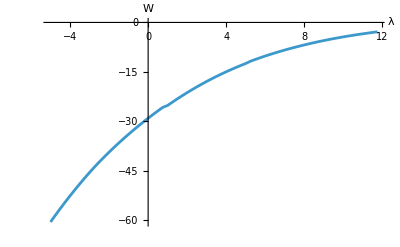
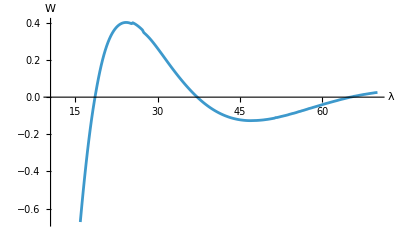

```mathematica
{ListLinePlot[valsW[[1;;68]],AxesLabel->{"λ","W"}],ListLinePlot[valsW[[68;;-1]],AxesLabel->{"λ","W"}]}
```

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,19}]]
```

{λ→18.6245}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,37}]]
```

{λ→37.2224}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,64}]]
```

{λ→65.0409}